## Formulae an

```mathematica
ExplainContractionCounts[g_,e_]:=Block[{
gBis=SortGraph[g], 
taken={e[[1]],e[[2]]},
comp=SortGraph[VertexDelete[VertexDelete[GraphComplement[g],e[[1]]],e[[2]]]],
nonEdges=0,
remainingNonEdges=0,
result},
result=Table[
If[!EdgeQ[gBis,e[[1]]<->v]&&!EdgeQ[gBis,e[[2]]<->v],
nonEdges++
]
,{v,Select[VertexList[gBis],!MemberQ[taken,#]&]}
];
remainingNonEdges=Length[EdgeList[comp]];
{nonEdges,remainingNonEdges}
]
```

```mathematica
MpgChain[g_]:=Block[{contract, result},
If[VertexCount[g]==3,Return[{ChromaticPolynomial[g,4]/24}]];
Table[
contract=EdgeContract[g,e];
If[MaximalPlanarQ[contract],
result=Prepend[MpgChain[contract],{e,ChromaticPolynomial[g,4]/24}];
Goto[stop]
]
,{e,EdgeList[g]}
];
Label[stop];
result
]
```

```mathematica
MpgChain3[g_]:=Block[{contract, result},
If[VertexCount[g]==3,Return[{ChromaticPolynomial[g,4]/24}]];
Table[
contract=EdgeContract[g,e];
If[MaximalPlanarQ[contract],
result=Prepend[MpgChain3[contract],ChromaticPolynomial[g,4]/24];
Goto[stop]
]
,{e,EdgeList[g]}
];
Label[stop];
result
]
```

```mathematica
Monitor[Select[Table[k->With[{l=Differences[Reverse[MpgChain3[ReadGrof[k]]]]},{Min[l],Max[l]}],{k,10}],#[[2]]≠{0,0}&],k]
```

{4→{0,3},6→{0,3},7→{0,3}}

```mathematica
cm=72/2.54;
```

```mathematica
MakeComplete[v_]:=Map[SortEdge[#[[1]]<->#[[2]]]&,Subsets[v,{2}]]
```

```mathematica
MakeComplete[Range[3]]
```

{1<->2,1<->3,2<->3}

```mathematica
BeautiGraph[g_]:=Graph[MakeComplete[VertexList[g]],GraphHighlight->EdgeList[GraphComplement[g]], GraphHighlightStyle->"Thick", VertexLabels->"Name", EdgeStyle->LightGray]
```

```mathematica
SolGraph[g_,sol_,newNeighbors_:{},highlight_:{}]:=Block[{
s=SymbolToSets[sol],
edges={},
colors={Red,Blue,Yellow,Green}, 
color=1,
high=Map[SortEdge,EdgeList[GraphComplement[g]]],
taken,
vertices={},
nonedges,
interesting,
 blackEdges
},
interesting=Select[VertexList[g],MemberQ[newNeighbors,#]&];
blackEdges=Map[#->Directive[Black,Thickness[0.01]]&,MakeComplete[interesting]];
nonedges=Length[high];
Table[
edges=Join[edges,Map[#->Directive[colors[[color]],Thick]&,MakeComplete[block]]];
vertices=Join[vertices,Map[#->colors[[color]]&,block]];
color+=1
,{block, s}
];
taken=Map[SortEdge,Map[First,edges]];
edges=Join[blackEdges,edges];
high=SetDifference[high,Join[taken,Map[First,blackEdges]]];
With[
{comp=Graph[
MakeComplete[VertexList[g]],
GraphHighlight->high,
GraphHighlightStyle->"Dotted",
EdgeStyle->edges, 
 VertexLabels->Map[If[MemberQ[highlight,#[[1]]],#[[1]]->Style[#[[2]],Red],#]&,Map[#->(If[MemberQ[newNeighbors,#],Framed[#],#])&,VertexList[g]]],
VertexStyle->vertices,
ImageSize->{12cm,12cm}
]},
Labeled[
{comp,Graph[Subgraph[comp,highlight],ImageSize->{5cm,5cm}]}
,
StringJoin[Map[ToString,{"vertices:",VertexCount[g], ", non-edges:",nonedges, ", taken:", Length[taken], ", not-taken:",nonedges- Length[taken]}]]
]
]
]
```

```mathematica
FindFullFormula4[Graph[plantri [[1]] ]]
```

{v19bx25cx37ax468,v19bx24cx357x68a,v18ax29bx357x46c,v18bx259x37ax46c,v18bx24cx36ax579,v18ax24bx36cx579,v17ax29bx35cx468,v17ax259x36cx48b,v179x25cx36ax48b,v179x24bx35cx68a}

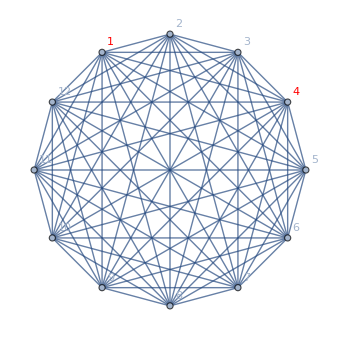
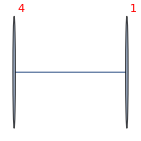
{-Graphics-,-Graphics-}vertices:12, non-edges:36, taken:12, not-taken:24

```mathematica
SolGraph[Graph[plantri [[1]] ],v19bx25cx37ax468,{1,2,3,4},{1,4}]
```

```mathematica
Clear[MpgChain2]
```

```mathematica
SymbolToColoring[First[FindFullFormula4[Graph[plantri [[1]] ]]]]
```

{1→RGBColor[1, 0, 0],9→RGBColor[1, 0, 0],11→RGBColor[1, 0, 0],2→RGBColor[0, 0, 1],5→RGBColor[0, 0, 1],12→RGBColor[0, 0, 1],3→RGBColor[1, 1, 0],7→RGBColor[1, 1, 0],10→RGBColor[1, 1, 0],4→RGBColor[0, 1, 0],6→RGBColor[0, 1, 0],8→RGBColor[0, 1, 0]}

```mathematica
MpgChain2[g_,glayout_:"TutteEmbedding",previous_:{}, positions_:Null,size_:{}, highlight_:{}]:=Block[{contract, result, coord, newPos=positions,newSize=size, layout, thegraph,form,graphs,first,newNeighbors},
If[VertexCount[g]==4,Return[{}]];
Table[
contract=EdgeContract[g,e];
If[MaximalPlanarQ[contract],
If[positions==Null,
layout = Graph[
SortGraph[g],
GraphLayout->glayout,
GraphHighlightStyle->"Thick",
ImageSize->{6 cm,6 cm}, 
VertexCoordinates->Automatic
];
newPos=First[AbsoluteOptions[layout, VertexCoordinates]][[2]];
newSize=First[AbsoluteOptions[layout, ImageSize]][[2]];
];
coord=newPos;(*Table[newPos[[k]],{k,VertexList[g]}];*)
form=FindFullFormula4[g];
newNeighbors=Intersection[VertexList[NeighborhoodGraph[g,e[[1]]]],VertexList[NeighborhoodGraph[g,e[[2]]]]];
If[form≠{},first=First[form];form=SymbolToColoring[first]];
thegraph=Graph[
Range[Length[newPos]],
EdgeList[g],
GraphHighlightStyle->"Thick",
VertexLabels->Map[If[MemberQ[highlight,#[[1]]],#[[1]]->Style[#[[2]],Directive[Red,Underlined]],#]&,Map[If[MemberQ[newNeighbors,#],#->Framed[#],If[MemberQ[previous,#],#->ToString[previous],#->#]]&,VertexList[g]]],
GraphHighlight->Select[CollectMPGEdges[g],#=!=e&],
VertexLabelStyle->Directive[Darker[Green],Italic,10],
ImageSize->newSize, 
AspectRatio->1,
EdgeStyle->{e->{Thick,Blue,Dashed}}, 
VertexStyle->form, 
VertexSize->Map[#->If[MemberQ[previous,#],Larger[Large],Large]&,VertexList[g]],
VertexCoordinates->coord
];
result=Prepend[MpgChain2[contract,glayout,{e[[1]],e[[2]]}, newPos,newSize,newNeighbors],{Labeled[
thegraph,{Style[ChromaticPolynomial[g,4]/24,Green ],Grid[Transpose[Map[{#,VertexDegree[g,#]}&,Sort[VertexList[g]]]],Frame->All]}],
FormatAdjacencyMatrix2[g,VertexList[NeighborhoodGraph[VertexContract[ thegraph,e],e[[1]]]]First[FindFullFormula4[VertexContract[ thegraph,e]]]],
Labeled[SolGraph[g,first,newNeighbors, highlight],highlight],
graphs=Table[
With[{sub=NeighborhoodGraph[ thegraph,v]},
Graph[EdgeList[sub],VertexSize->Medium,GraphLayout->"SpringElectricalEmbedding",VertexStyle->Select[form,MemberQ[VertexList[sub],#[[1]]]&],VertexLabels->"Name",EdgeStyle->{e->{Thick,Blue,Dashed}},ImageSize->{3 cm,3 cm}]
],
{v,{e[[1]],e[[2]]}}
];
With[
{sub=GraphUnion[graphs[[1]],graphs[[2]]]},
Labeled[Graph[EdgeList[sub],VertexSize->Large,GraphLayout->"PlanarEmbedding",VertexStyle->Select[form,MemberQ[VertexList[sub],#[[1]]]&],VertexLabels->"Name",EdgeStyle->{e->{Thick,Blue,Dashed}},ImageSize->{4 cm,4 cm}],e]]

,

Column[
With[
{sub=NeighborhoodGraph[VertexContract[ thegraph,e],e[[1]]]},
{
Graph[EdgeList[sub],VertexSize->Large,GraphLayout->"PlanarEmbedding",VertexStyle->Select[form,MemberQ[VertexList[sub],#[[1]]]&],VertexLabels->"Name",ImageSize->{4 cm,4 cm}]
,
form=FindFullFormula4[sub];
If[form≠{},form=SymbolToColoring[First[form]]];
Graph[EdgeList[sub],VertexSize->Large,GraphLayout->"PlanarEmbedding",VertexStyle->Select[form,MemberQ[VertexList[sub],#[[1]]]&],VertexLabels->"Name",ImageSize->{4 cm,4 cm}]
}]
]}];
Goto[stop]
]
,{e,EdgeList[g]}
];
Label[stop];
result
]
```

## experiments come

```mathematica
FindFullFormula4[VertexContract[Graph[plantri [[1]] ],{1,2}]]
```

{v19bx37ax468x5c,v19bx37ax46cx58,v1cx36ax48bx579,v1ax36cx48bx579,v19bx357x4cx68a,v19bx35cx47x68a,v19bx357x46cx8a,v19bx35cx468x7a}

```mathematica
MpgChain2[Graph[plantri [[1]] ] ]
```

$Aborted

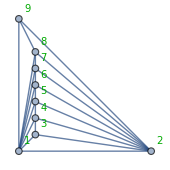
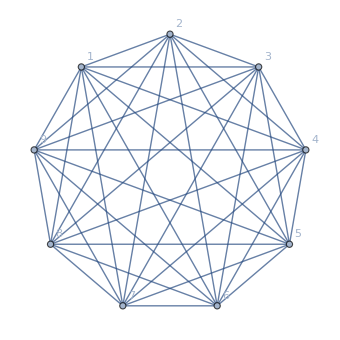
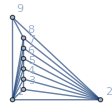
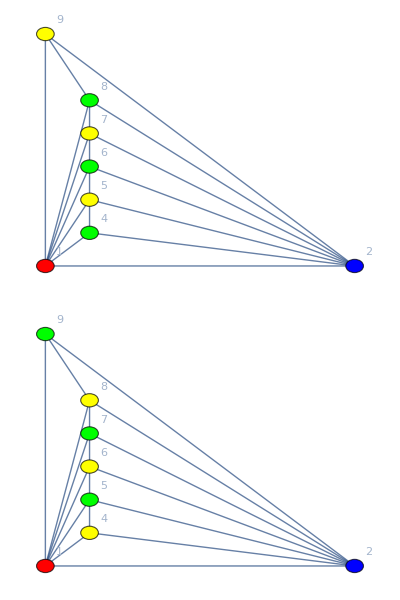
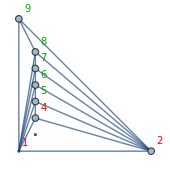
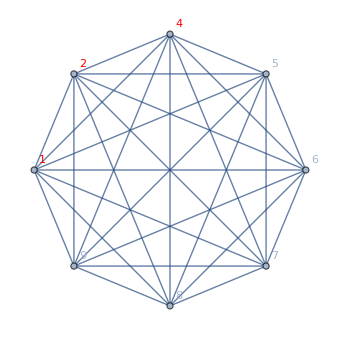
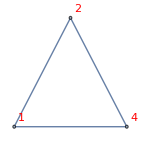
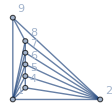
{{-Graphics-{1,1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9
8 | 8 | 3 | 4 | 4 | 4 | 4 | 4 | 3},( | 1 | 2 | 3 | 5 | 7 | 9 | 4 | 6 | 8
1 | ◆ | ● | ● | ● | ● | ● | ● | ● | ●
2 | ● | ◆ | ● | ● | ● | ● | ● | ● | ●
3 | ● | ● | ◆ | ● | ● | ● | ● | ● | ●
5 | ● | ● | ● | ◆ | ● | ● | ● | ● | ●
7 | ● | ● | ● | ● | ◆ | ● | ● | ● | ●
9 | ● | ● | ● | ● | ● | ◆ | ● | ● | ●
4 | ● | ● | ● | ● | ● | ● | ◆ | ● | ●
6 | ● | ● | ● | ● | ● | ● | ● | ◆ | ●
8 | ● | ● | ● | ● | ● | ● | ● | ● | ◆),{-Graphics-,-Graphics-}vertices:9, non-edges:15, taken:9, not-taken:6{},-Graphics-1<->3,-Graphics-},{-Graphics-{1,1 | 2 | 4 | 5 | 6 | 7 | 8 | 9
7 | 7 | 3 | 4 | 4 | 4 | 4 | 3},( | 1 | 2 | 4 | 6 | 8 | 5 | 7 | 9
1 | ◆ | ● | ● | ● | ● | ● | ● | ●
2 | ● | ◆ | ● | ● | ● | ● | ● | ●
4 | ● | ● | ◆ | ● | ● | ● | ● | ●
6 | ● | ● | ● | ◆ | ● | ● | ● | ●
8 | ● | ● | ● | ● | ◆ | ● | ● | ●
5 | ● | ● | ● | ● | ● | ◆ | ● | ●
7 | ● | ● | ● | ● | ● | ● | ◆ | ●
9 | ● | ● | ● | ● | ● | ● | ● | ◆),{-Graphics-,-Graphics-}vertices:8, non-edges:10, taken:6, not-taken:4{1,2,3,4},-Graphics-2<->4,-Graphics-},{-Graphics-{1,1 | 2 | 5 | 6 | 7 | 8 | 9
6 | 6 | 3 | 4 | 4 | 4 | 3},( | 1 | 2 | 5 | 7 | 9 | 6 | 8
1 | ◆ | ● | ● | ● | ● | ● | ●
2 | ● | ◆ | ● | ● | ● | ● | ●
5 | ● | ● | ◆ | ● | ● | ● | ●
7 | ● | ● | ● | ◆ | ● | ● | ●
9 | ● | ● | ● | ● | ◆ | ● | ●
6 | ● | ● | ● | ● | ● | ◆ | ●
8 | ● | ● | ● | ● | ● | ● | ◆),{-Graphics-,-Graphics-}vertices:7, non-edges:6, taken:4, not-taken:2{1,2,4,5},-Graphics-5<->6,-Graphics-},{-Graphics-{1,1 | 2 | 5 | 7 | 8 | 9
5 | 5 | 3 | 4 | 4 | 3},( | 1 | 2 | 5 | 8 | 7 | 9
1 | ◆ | ● | ● | ● | ● | ●
2 | ● | ◆ | ● | ● | ● | ●
5 | ● | ● | ◆ | ● | ● | ●
8 | ● | ● | ● | ◆ | ● | ●
7 | ● | ● | ● | ● | ◆ | ●
9 | ● | ● | ● | ● | ● | ◆),{-Graphics-,-Graphics-}vertices:6, non-edges:3, taken:2, not-taken:1{1,2,5,6},-Graphics-7<->8,-Graphics-},{-Graphics-{1,1 | 2 | 5 | 7 | 9
4 | 4 | 3 | 4 | 3},( | 1 | 2 | 5 | 9 | 7
1 | ◆ | ● | ● | ● | ●
2 | ● | ◆ | ● | ● | ●
5 | ● | ● | ◆ | ● | ●
9 | ● | ● | ● | ◆ | ●
7 | ● | ● | ● | ● | ◆),{-Graphics-,-Graphics-}vertices:5, non-edges:1, taken:1, not-taken:0{1,2,7,8},-Graphics-1<->9,-Graphics-}}

```mathematica
MpgChain2[MinimalGraph[8] ,"PlanarEmbedding"]
```

```mathematica
MpgChain2[MinimalGraph2[10] ,"PlanarEmbedding"]
```